# DTQW Optimizada (Wang et al.)

## Modelo de caminata cuántica

Implementación de caminata cuántica discreta en el tiempo basada en el modelo presentado por Wang et al. en [1]. Dónde la caminata está dada por

-Graphics-

dónde

-Graphics-

## Definiciones

### Contenido externo

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

### Constantes

```mathematica
α=π/6.
```

0.523599

### Operadores optimizados

```mathematica
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
```

```mathematica
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
```

```mathematica
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
```

```mathematica
FuzzyOperator[n_]:=RotateLeft[IdentityMatrix[n,SparseArray]]
```

```mathematica
DTQW[rho_,n_]:=Module[{ρ},
ρ=rho;
Do[ρ=Chop[#.ArrayPad[ρ,{{0,2},{0,2}}].ConjugateTranspose[#]]&[UnitaryOperator[t+1]],{t,n}];
ρ
]
```

```mathematica
FuzzyDTQW[rho_,n_,p_]:=Module[{ρ,pre},
ρ=rho;
Do[
pre=(#.ArrayPad[ρ,{{0,2},{0,2}}].ConjugateTranspose[#])&[UnitaryOperator[t+1]];
ρ=Chop[(1-p)*pre+p*#.pre.ConjugateTranspose[#]]&[RotateLeft[IdentityMatrix[2*t+2,SparseArray],2]],
{t,n}
];
ρ
]
```

### Una caminata

```mathematica
rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
AbsoluteTiming[rho=DTQW[rho,150];]
```

{2.71099,Null}

```mathematica
probs=Diagonal@MatrixPartialTrace[rho,2,{151,2}];
```

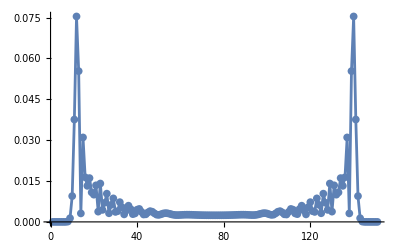

```mathematica
ListLinePlot[probs,
PlotRange->All,
Mesh->All
]
```

### Fuzzy walk 1

```mathematica
rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
```

```mathematica
AbsoluteTiming[rho=FuzzyDTQW[rho,150,0.01];]
```

{7.37522,Null}

```mathematica
probs2=Diagonal@MatrixPartialTrace[rho,2,{151,2}];
```

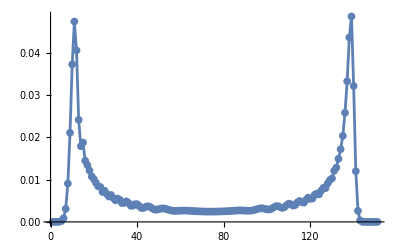

```mathematica
ListLinePlot[probs2,
PlotRange->All,
Mesh->All
]
```

### Fuzzy walk 2

```mathematica
rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
```

```mathematica
AbsoluteTiming[rho=FuzzyDTQW[rho,150,0.1];]
```

{7.18109,Null}

```mathematica
probs2=Diagonal@MatrixPartialTrace[rho,2,{151,2}];
```

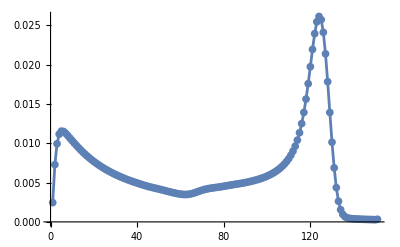

```mathematica
ListLinePlot[probs2,
PlotRange->All,
Mesh->All
]
```

### Una caminata con fuzzy al final

```mathematica
rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
AbsoluteTiming[rho=DTQW[rho,150];]
```

{2.74512,Null}

```mathematica
probs3=Diagonal@(#.MatrixPartialTrace[rho,2,{151,2}].ConjugateTranspose[#])&[FuzzyOperator[151]];
```

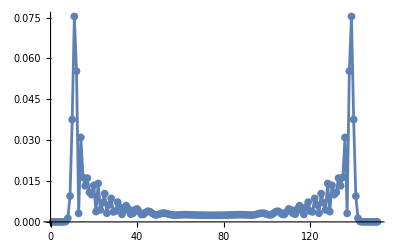

```mathematica
ListLinePlot[probs3,
PlotRange->All,
Mesh->All
]
```

```mathematica
RotateLeft[Chop[probs]]==Chop[probs3]
```

True

### Muchas probabilidades

#### Con p entre 0 y 1

```mathematica
AbsoluteTiming[mprobs=Module[{n,rho,rhof},
(* parametros *)
n=150;

rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
Table[
AbsoluteTiming[rhof=FuzzyDTQW[rho,n,p];];
Diagonal@MatrixPartialTrace[rhof,2,{n+1,2}],
{p,0,1,0.1}
]
];]
```

{51.8209,Null}

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/many-probabilities.gif",Table[
ListLinePlot[mprobs[[n]],
PlotRange->All,
Mesh->All,
PlotLabel->TraditionalForm[p==(n-1)*0.1]
],{n,1,11,1}
],
"DisplayDurations"->ConstantArray[0.6,11]
]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/many-probabilities.gif

#### Con p entre 0.9 y 1

```mathematica
AbsoluteTiming[mprobs2=Module[{n,rho,rhof},
(* parametros *)
n=150;

rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
Table[
AbsoluteTiming[rhof=FuzzyDTQW[rho,n,p];];
Diagonal@MatrixPartialTrace[rhof,2,{n+1,2}],
{p,0.9,1,0.01}
]
];]
```

{55.4749,Null}

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/many-probabilities2.gif",Table[
ListLinePlot[mprobs2[[n]],
PlotRange->All,
Mesh->All,
PlotLabel->TraditionalForm[p==0.9+(n-1)*0.01]
],{n,1,11,1}
],
"DisplayDurations"->ConstantArray[0.6,11]
]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/many-probabilities2.gif

### Evolución temporal

```mathematica
AbsoluteTiming[evo=Module[{n,p,uni,rho,probs,mean,sd},
(* parametros *)
n=51;
p=1;

rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
probs=ConstantArray[0,{n,n}];
mean=ConstantArray[0,n];
sd=ConstantArray[0,n];

Do[
probs[[t,1;;t]]=Chop[Diagonal@MatrixPartialTrace[rho,2,{t,2}]];
mean[[t]]=a;(*seguir aquí*)

uni=(#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#])&[UnitaryOperator[t+1]];
rho=Chop[(1-p)*uni+p*#.uni.ConjugateTranspose[#]]&[RotateLeft[IdentityMatrix[2*t+2,SparseArray],2]],
{t,n}
];
probs
];]
```

{1.30101,Null}

```mathematica
Manipulate[ListLinePlot[evo[[n]],
PlotRange->All,
Mesh->All,
PlotLabel->StringForm["Step #``",n]
],{n,1,51,1}]
```

Part::partd: Part specification evo[[51]] is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression Annotation[51, Charting`Private`Tag#2]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

ListLinePlot::lpn: 
   Annotation[evo, Charting`Private`Tag#1][[Annotation[51, 
      Charting`Private`Tag#2]]] is not a list of numbers or pairs of numbers.

Part::partd: Part specification evo[[51]] is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression Annotation[51, Charting`Private`Tag#2]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

ListLinePlot::lpn: 
   Annotation[evo, Charting`Private`Tag#1][[Annotation[51, 
      Charting`Private`Tag#2]]] is not a list of numbers or pairs of numbers.

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/time-evolution.gif",Join[
Table[ListLinePlot[evo[[n]],
PlotRange->{All,{0,1}},
Mesh->All,
PlotLabel->StringForm["Step #``",n]
],{n,1,5,1}],
Table[ListLinePlot[evo[[n]],
PlotRange->{All,{0,0.3}},
Mesh->All,
PlotLabel->StringForm["Step #``",n]
],{n,5,20,1}],
Table[ListLinePlot[evo[[n]],
PlotRange->{All,{0,0.1}},
Mesh->All,
PlotLabel->StringForm["Step #``",n]
],{n,20,100,1}],
Table[ListLinePlot[evo[[n]],
PlotRange->{All,{0,0.035}},
Mesh->All,
PlotLabel->StringForm["Step #``",n]
],{n,100,151,1}]
],
"DisplayDurations"->ConstantArray[0.3,154]
]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/time-evolution.gif

## Extras

```mathematica
f[x_?MatrixQ]:="hola"
```

```mathematica
f[{{a,b},{c,d}}]
```

hola

```mathematica
ss=Ket[{1,0}]
```

1,0

```mathematica
vs=Ket[{a,b}]/5+Ket[{c,d}]+2Ket[{e,f}]
```

(a,b)/5+c,d+2 e,f

```mathematica
dm=Ket[{a,b}].Bra[{z,y}]+3Ket[{c,d}].Bra[{x,w}]/2+Ket[{e,f}].Bra[{v,u}]
```

a,b.z,y+3/2 c,d.x,w+e,f.v,u

```mathematica
Cases[#,_Ket,Infinity]&/@{ss,vs,dm}//Column
```

{}
{a,b,c,d,e,f}
{a,b,c,d,e,f}

## Referencias

[1] Q.-Q. Wang et al., “Efficient learning of mixed-state tomography for photonic quantum walk”, Sci. Adv., vol. 10, núm. 11, p. eadl4871, mar. 2024, doi: 10.1126/sciadv.adl4871.

## ...

```mathematica
MatrixForm[fm=KroneckerProduct[RotateLeft[IdentityMatrix[3]],IdentityMatrix[2]]]
```

(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[matb=Table[b[i,j],{i,4},{j,4}]]
```

(b[1,1] | b[1,2] | b[1,3] | b[1,4]
b[2,1] | b[2,2] | b[2,3] | b[2,4]
b[3,1] | b[3,2] | b[3,3] | b[3,4]
b[4,1] | b[4,2] | b[4,3] | b[4,4])

```mathematica
(mat=Table[a[i,j],{i,8},{j,8}])//MatrixForm
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4] | a[1,5] | a[1,6] | a[1,7] | a[1,8]
a[2,1] | a[2,2] | a[2,3] | a[2,4] | a[2,5] | a[2,6] | a[2,7] | a[2,8]
a[3,1] | a[3,2] | a[3,3] | a[3,4] | a[3,5] | a[3,6] | a[3,7] | a[3,8]
a[4,1] | a[4,2] | a[4,3] | a[4,4] | a[4,5] | a[4,6] | a[4,7] | a[4,8]
a[5,1] | a[5,2] | a[5,3] | a[5,4] | a[5,5] | a[5,6] | a[5,7] | a[5,8]
a[6,1] | a[6,2] | a[6,3] | a[6,4] | a[6,5] | a[6,6] | a[6,7] | a[6,8]
a[7,1] | a[7,2] | a[7,3] | a[7,4] | a[7,5] | a[7,6] | a[7,7] | a[7,8]
a[8,1] | a[8,2] | a[8,3] | a[8,4] | a[8,5] | a[8,6] | a[8,7] | a[8,8])

```mathematica
RotateLeft[RotateLeft[#,2]&/@mat,2]//MatrixForm
```

(a[3,3] | a[3,4] | a[3,5] | a[3,6] | a[3,7] | a[3,8] | a[3,1] | a[3,2]
a[4,3] | a[4,4] | a[4,5] | a[4,6] | a[4,7] | a[4,8] | a[4,1] | a[4,2]
a[5,3] | a[5,4] | a[5,5] | a[5,6] | a[5,7] | a[5,8] | a[5,1] | a[5,2]
a[6,3] | a[6,4] | a[6,5] | a[6,6] | a[6,7] | a[6,8] | a[6,1] | a[6,2]
a[7,3] | a[7,4] | a[7,5] | a[7,6] | a[7,7] | a[7,8] | a[7,1] | a[7,2]
a[8,3] | a[8,4] | a[8,5] | a[8,6] | a[8,7] | a[8,8] | a[8,1] | a[8,2]
a[1,3] | a[1,4] | a[1,5] | a[1,6] | a[1,7] | a[1,8] | a[1,1] | a[1,2]
a[2,3] | a[2,4] | a[2,5] | a[2,6] | a[2,7] | a[2,8] | a[2,1] | a[2,2])